Here we define the boat and the water using ImplicitRegion, and the underwater section as the intersection of the boat and the water using RegionIntersection - we don’t have to use this function - we could write our own definition of the underwater section, but if you look at the expression you will notice that it is exactly what you would have defined anyway. Notice that we are using a sloped line to represent the water, and a variable d that is the intersection with the y-axis. It would be a lot better to use a variable that is the depth of the water, i.e. perpendicular to the line, but let’s leave that for another day. Since Manipulate can’t “see” d inside of water and under, we have to replace d with a local variable, which we call dd, so that Manipulate can do its work. We’ve set the name of the variable dd to be draft, and we’ve assigned an initial value of 1 with a range from -2 to 4. You have to play with this initially, because it is not clear to begin with what the correct range is. At this point we’ve hard-coded 30 degrees - we will eventually want this to be a variable. We would need to work a bit harder to find the precise set of d values that will “cover” the whole boat.

```mathematica
Clear["Global`*"]
```

```mathematica
boat = ImplicitRegion[x^2/2<y<2&&-2<x<2&&0<y<2,{x,y}]
water = ImplicitRegion[y<Tan[30 Degree]*x+d&&-2<x<2&&-2<y<4,{x,y}]
under = RegionIntersection[boat,water]
Manipulate[RegionPlot[{water/.{d->dd},boat,under/.{d->dd}},AspectRatio->Automatic],{{dd,0,"draft"},-2,4,Appearance->"Labeled"}]
```

ImplicitRegion[x^2/2<y<2&&-2<x<2&&0<y<2,{x,y}]

ImplicitRegion[y<d+x/(√3)&&-2<x<2&&-2<y<4,{x,y}]

ImplicitRegion[-2<x<2&&0<y<2&&x^2<2 y&&3 d+√3 x>3 y,{x,y}]

Here we will compute the mass of the boat and the mass of the displaced water in the underwater section as we vary the position of the water from -2 to 4 - we pass this into the Integrate function as an assumption - it just cleans up the answer. Notice that the answer is a function of d and it takes a different form depending on a couple of intervals for d. If you look at these closely they make a lot of sense. You will see that the minimum d value that returns a non-zero displacement is d = -1/6: this corresponds to the waterline being tangent to the boat. As you increase d, the water will intersect two part of the hull until you reach d = 2/3(3 - √3), after which the water intersects the hull and the deck. You will also notice that the displacement becomes constant after d = 2/3(3 + √3): this corresponds to the waterline leaving the top left of the boat.

```mathematica
mass = 10*Integrate[300,{x,y}∈boat]+5000
disp = 10*Integrate[1000,{x,y}∈under,Assumptions->{-2<d<4}]
```

21000

10 (Piecewise[{{2000/27 (√3 √(1+6 d)+6 √3 d √(1+6 d)), -1/6<d≤-2/3 (-3+√3)}, {-500/27 (-144+110 √3-90 √3 d+27 √3 d^2-2 √3 √(1+6 d)-12 √3 d √(1+6 d)), -2/3 (-3+√3)<d<2/(√3)||2/(√3)≤d<2/3 (3+√3)}, {1000 (2 (2+√3 (-2+d))+1/6 (-8-3 √3 (-2+d)^3)), d==2/3 (3+√3)}, {16000/3, d>2/3 (3+√3)}, {0, True}}])

For validation, we plot the displacement as a function of d, and then we solve for the waterline by finding the value of d where the displacement equals the mass of the boat. Notice that you do get an exact solution for this case, but it starts to run on quite a bit! The numerical value looks good.

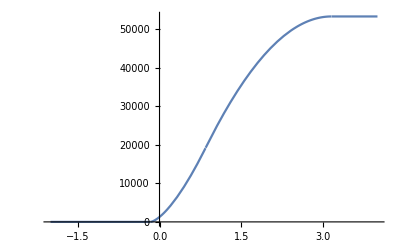

{{d→53/27+1/2 √(2164/729+68/(45 √3)-133196/135 (2/(3 (30369690-7339223 √3+√(1544547828343275-357173285922180 √3))))^(1/3)-(1768 (2/(30369690-7339223 √3+√(1544547828343275-357173285922180 √3)))^(1/3))/(9 3^(5/6))+2/135 (2/3)^(2/3) (30369690-7339223 √3+√(1544547828343275-357173285922180 √3))^(1/3))-1/2 √(31544/729-68/(45 √3)-(2 (113400-4590 √3))/6075+133196/135 (2/(3 (30369690-7339223 √3+√(1544547828343275-357173285922180 √3))))^(1/3)+(1768 (2/(30369690-7339223 √3+√(1544547828343275-357173285922180 √3)))^(1/3))/(9 3^(5/6))-2/135 (2/3)^(2/3) (30369690-7339223 √3+√(1544547828343275-357173285922180 √3))^(1/3)+(-(8 (-165600+15300 √3))/6075-212/27 (-44944/729+(4 (113400-4590 √3))/6075))/(4 √(2164/729+68/(45 √3)-133196/135 (2/(3 (30369690-7339223 √3+√(1544547828343275-357173285922180 √3))))^(1/3)-(1768 (2/(30369690-7339223 √3+√(1544547828343275-357173285922180 √3)))^(1/3))/(9 3^(5/6))+2/135 (2/3)^(2/3) (30369690-7339223 √3+√(1544547828343275-357173285922180 √3))^(1/3))))}}

0.909465

```mathematica
Plot[disp,{d,-2,4}]
waterline = Solve[disp==mass,d,Reals]
draft = N[d/.waterline[[1]]]
```

Now we turn our attention to the center of buoyancy of the submerged region. It’s still possible to compute the COB for any draft, and again it is divided into intervals for d. We then evaluate the COB for d set to the draft.

```mathematica
cob = 10*Integrate[1000*{x,y},{x,y}∈under, Assumptions->{-2<d<4}]/disp
cob/.{d->draft}
```

{Piecewise[{{2000/27 (√(1+6 d)+6 d √(1+6 d)), -1/6<d≤-2/3 (-3+√3)}, {500/27 (-110+306 d-189 d^2+27 d^3+2 √(1+6 d)+12 d √(1+6 d)), -2/3 (-3+√3)<d<2/(√3)||2/(√3)≤d<2/3 (3+√3)}, {125 (64-192 d+192 d^2-72 d^3+9 d^4), d==2/3 (3+√3)}, {0, True}}]/Piecewise[{{2000/27 (√3 √(1+6 d)+6 √3 d √(1+6 d)), -1/6<d≤-2/3 (-3+√3)}, {-500/27 (-144+110 √3-90 √3 d+27 √3 d^2-2 √3 √(1+6 d)-12 √3 d √(1+6 d)), -2/3 (-3+√3)<d<2/(√3)||2/(√3)≤d<2/3 (3+√3)}, {1000 (2 (2+√3 (-2+d))+1/6 (-8-3 √3 (-2+d)^3)), d==2/3 (3+√3)}, {16000/3, d>2/3 (3+√3)}, {0, True}}],Piecewise[{{400/81 (4 √3 √(1+6 d)+33 √3 d √(1+6 d)+54 √3 d^2 √(1+6 d)), -1/6<d≤-2/3 (-3+√3)}, {-100/81 (-2592+2168 √3-1530 √3 d+270 √3 d^2+135 √3 d^3-8 √3 √(1+6 d)-66 √3 d √(1+6 d)-108 √3 d^2 √(1+6 d)), -2/3 (-3+√3)<d<2/(√3)||2/(√3)≤d<2/3 (3+√3)}, {500 (4 (2+√3 (-2+d))+1/20 (-32-9 √3 (-2+d)^5)), d==2/3 (3+√3)}, {6400, d>2/3 (3+√3)}, {0, True}}]/Piecewise[{{2000/27 (√3 √(1+6 d)+6 √3 d √(1+6 d)), -1/6<d≤-2/3 (-3+√3)}, {-500/27 (-144+110 √3-90 √3 d+27 √3 d^2-2 √3 √(1+6 d)-12 √3 d √(1+6 d)), -2/3 (-3+√3)<d<2/(√3)||2/(√3)≤d<2/3 (3+√3)}, {1000 (2 (2+√3 (-2+d))+1/6 (-8-3 √3 (-2+d)^3)), d==2/3 (3+√3)}, {16000/3, d>2/3 (3+√3)}, {0, True}}]}

{0.574017,0.809448}

Although we could note use a Manipulate and show the COB for any water depth, we will end this section by simply showing the situation in static equilibrium. Any expression that contains d should have d replaced by the actual draft.

```mathematica
Show[RegionPlot[{water/.{d->draft},boat,under/.{d->draft}},AspectRatio->Automatic],ListPlot[{cob/.{d->draft}}]]
```

-Graphics-

Now that we have the COB, we can go ahead and compute the righting moment .....